## NTissueCells-example.nb NTissueCells,NTissueEdges,NTissueVertices

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51e (11 June 2017)) loaded Sun 11 Jun 2017 18:44:25
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

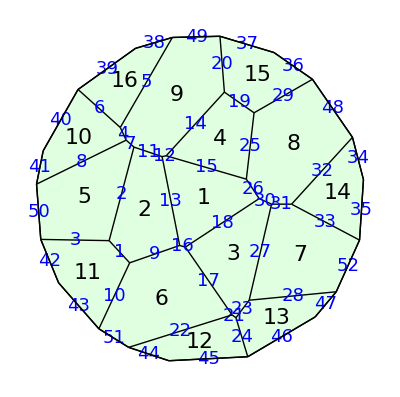

```mathematica
w=TemplateRandomCircularGrid[16,100];
ShowTissue[w, "CellNumbers"-> True, 
"CellNumberStyle"-> {FontSize-> 22}, 
"EdgeNumbers"-> True, "EdgeNumberStyle"-> {Blue, Background-> Pink, FontFamily-> "Verdana", FontSize-> 18}]
```

```mathematica
NTissueCells[w]
```

16

```mathematica
NTissueVertices[w]
```

37

```mathematica
NTissueEdges[w]
```

52

```mathematica
Length/@w
```

Tissue[37,52,16]